```mathematica
description="Intermediate calculations";
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)";
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
```

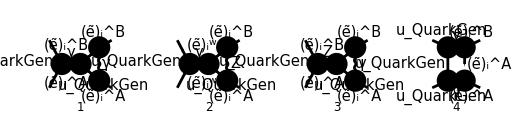

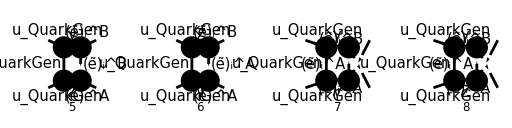

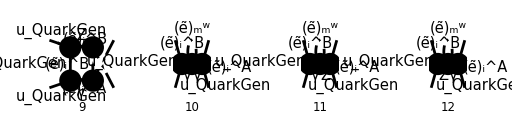

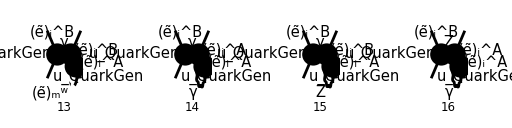

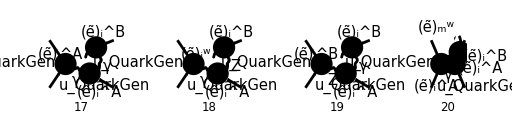

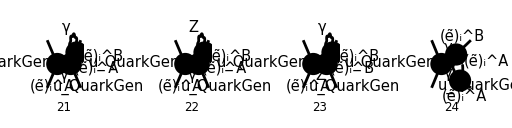

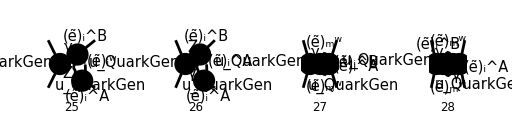

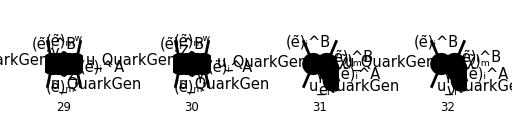

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles}],
{F[3,{QuarkGen}],-F[3,{QuarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSMCT,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4],S[5],S[6],S[11],S[13],S[14],V[3]},
LastSelections->{V[1],S[12]}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

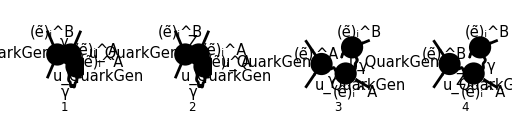

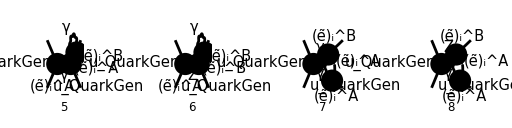

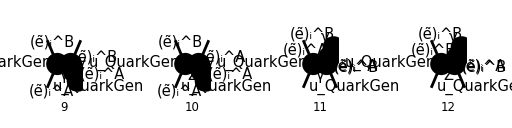

```mathematica
diags[1]=DiagramExtract[diags[0],{14,16,17,19,21,23,24,26,33,35,38,40}];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

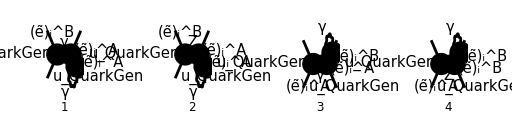

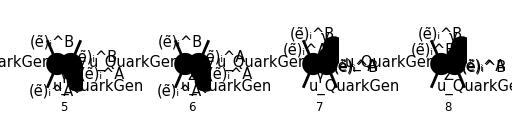

```mathematica
diags[2]=DiagramExtract[diags[1],{1,2,5,6,9,10,11,12}];
Paint[
diags[2],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[2]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
ChangeDimension->D,
UndoChiralSplittings->True,
Contract->True,
DropSumOver->True,
SMP->True,
List->True
]/.{MQU[QuarkGen]->0}
```

{-(ⅈ D (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(24 π^4 (k_1+k_2)^2 LoopMom1^2 (k_2^2-(MSf(A,2,i))^2)),-((D (φ(-p_2)).((2 ⅈ (γ·(k_2-k_1)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k_2-k_1)).(γ̄)^7 (1-4 (cos(θ_W))^2) e δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (1-2 (cos(θ_W))^2) USf(2,i)(A,1)))/(32 π^4 LoopMom1^2 (k_2^2-(MSf(A,2,i))^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),(ⅈ D (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(24 π^4 (k_1+k_2)^2 LoopMom1^2 (k_1^2-(MSf(A,2,i))^2)),(D (φ(-p_2)).((2 ⅈ (γ·(k_1-k_2)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k_1-k_2)).(γ̄)^7 (1-4 (cos(θ_W))^2) e δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (1-2 (cos(θ_W))^2) USf(2,i)(A,1)))/(32 π^4 LoopMom1^2 (k_1^2-(MSf(B,2,i))^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)) IndexDelta(A,B) (-k_2^2+2 (k_2·LoopMom1)-LoopMom1^2) e^4 δ_Col1Col2)/(24 π^4 (LoopMom1^2-(MSf(A,2,i))^2).(k_2+LoopMom1)^2 (k_1+k_2)^2 (k_2^2-(MSf(B,2,i))^2)),-(((φ(-p_2)).((2 ⅈ (γ·(k_2-k_1)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k_2-k_1)).(γ̄)^7 (1-4 (cos(θ_W))^2) e δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k_2^2+2 (k_2·LoopMom1)-LoopMom1^2) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (1-2 (cos(θ_W))^2) USf(2,i)(A,1)))/(32 π^4 (LoopMom1^2-(MSf(A,2,i))^2).(k_2+LoopMom1)^2 (k_2^2-(MSf(A,2,i))^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),(ⅈ (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)) IndexDelta(A,B) (-k_1^2+2 (k_1·LoopMom1)-LoopMom1^2) e^4 δ_Col1Col2)/(24 π^4 (LoopMom1^2-(MSf(B,2,i))^2).(k_1+LoopMom1)^2 (k_1+k_2)^2 (k_1^2-(MSf(A,2,i))^2)),((φ(-p_2)).((2 ⅈ (γ·(k_1-k_2)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k_1-k_2)).(γ̄)^7 (1-4 (cos(θ_W))^2) e δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k_1^2+2 (k_1·LoopMom1)-LoopMom1^2) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (1-2 (cos(θ_W))^2) USf(2,i)(A,1)))/(32 π^4 (LoopMom1^2-(MSf(B,2,i))^2).(k_1+LoopMom1)^2 (k_1^2-(MSf(B,2,i))^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))}

```mathematica
Mγ[0]=Total[Mlist[0][[{1,3,5,7}]] 3/2 SMP["e_Q"]];
MZ[0]=Total[Mlist[0][[{2,4,6,8}]]];
```

Rewrite the “chiral coefficients” into and  (see p.164 in Richardson). Note that the amplitudes in FeynArts used up quarks.

```mathematica
MZ[1]=MZ[0]/.{4 SMP["sin_W"]^2-3:>12 Zql};
MZ[2]=MZ[1]/.{SMP["sin_W"]/SMP["cos_W"]:>3 Zqr / (SMP["sin_W"] SMP["cos_W"])}
```

(D e^3 ((1-2 (cos(θ_W))^2) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]+2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]) (φ(-p_2)).((ⅈ e δ_Col1Col2 (1-4 (cos(θ_W))^2) (γ·(k_1-k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))+(2 ⅈ e Zqr δ_Col1Col2 (γ·(k_1-k_2)).(γ̄)^6)/((cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(32 π^4 LoopMom1^2 (cos(θ_W)) (sin(θ_W)) (k_1^2-(MSf(B,2,i))^2) ((k_1+k_2)^2-m_Z^2))-(D e^3 ((1-2 (cos(θ_W))^2) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]+2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]) (φ(-p_2)).((ⅈ e δ_Col1Col2 (1-4 (cos(θ_W))^2) (γ·(k_2-k_1)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))+(2 ⅈ e Zqr δ_Col1Col2 (γ·(k_2-k_1)).(γ̄)^6)/((cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(32 π^4 LoopMom1^2 (cos(θ_W)) (sin(θ_W)) (k_2^2-(MSf(A,2,i))^2) ((k_1+k_2)^2-m_Z^2))+(e^3 (2 (k_1·LoopMom1)-LoopMom1^2-k_1^2) ((1-2 (cos(θ_W))^2) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]+2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]) (φ(-p_2)).((ⅈ e δ_Col1Col2 (1-4 (cos(θ_W))^2) (γ·(k_1-k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))+(2 ⅈ e Zqr δ_Col1Col2 (γ·(k_1-k_2)).(γ̄)^6)/((cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(32 π^4 (cos(θ_W)) (sin(θ_W)) (k_1^2-(MSf(B,2,i))^2) ((k_1+k_2)^2-m_Z^2) (LoopMom1^2-(MSf(B,2,i))^2).(k_1+LoopMom1)^2)-(e^3 (2 (k_2·LoopMom1)-LoopMom1^2-k_2^2) ((1-2 (cos(θ_W))^2) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]+2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]) (φ(-p_2)).((ⅈ e δ_Col1Col2 (1-4 (cos(θ_W))^2) (γ·(k_2-k_1)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))+(2 ⅈ e Zqr δ_Col1Col2 (γ·(k_2-k_1)).(γ̄)^6)/((cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(32 π^4 (cos(θ_W)) (sin(θ_W)) (k_2^2-(MSf(A,2,i))^2) ((k_1+k_2)^2-m_Z^2) (LoopMom1^2-(MSf(A,2,i))^2).(k_2+LoopMom1)^2)

Rewrite the sfermion mixing matrices USf into (again: see p.164 in Richardson), using that the mixing matrices are real, and .

```mathematica
MZ[3]=MZ[2]//.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
MZ[4]=MZ[3]//.{2SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2 ZliAB}//Simplify
```

(e^3 ((-2 (cos(θ_W))^2-2 (sin(θ_W))^2+1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]+2 (sin(θ_W))^2 A,B) (1/(k_2^2-(MSf(A,2,i))^2)((-2 (k_2·LoopMom1)+LoopMom1^2+k_2^2)/((LoopMom1^2-(MSf(A,2,i))^2).(k_2+LoopMom1)^2)-D/LoopMom1^2) (φ(-p_2)).(ⅈ e δ_Col1Col2 ((1-4 (cos(θ_W))^2) (γ·(k_2-k_1)).(γ̄)^7+12 Zqr (γ·(k_2-k_1)).(γ̄)^6))/(6 (cos(θ_W)) (sin(θ_W))).(φ(p_1))+1/(k_1^2-(MSf(B,2,i))^2)(D/LoopMom1^2-(-2 (k_1·LoopMom1)+LoopMom1^2+k_1^2)/((LoopMom1^2-(MSf(B,2,i))^2).(k_1+LoopMom1)^2)) (φ(-p_2)).(ⅈ e δ_Col1Col2 ((1-4 (cos(θ_W))^2) (γ·(k_1-k_2)).(γ̄)^7+12 Zqr (γ·(k_1-k_2)).(γ̄)^6))/(6 (cos(θ_W)) (sin(θ_W))).(φ(p_1))))/(32 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))

Combine back amplitudes

```mathematica
M[0]=Mγ[0]+MZ[4]//Simplify
```

1/(32 π^4)e^3 ((((-2 (cos(θ_W))^2-2 (sin(θ_W))^2+1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]+2 (sin(θ_W))^2 A,B) (1/(k_2^2-(MSf(A,2,i))^2)((-2 (k_2·LoopMom1)+LoopMom1^2+k_2^2)/((LoopMom1^2-(MSf(A,2,i))^2).(k_2+LoopMom1)^2)-D/LoopMom1^2) (φ(-p_2)).(ⅈ e δ_Col1Col2 ((1-4 (cos(θ_W))^2) (γ·(k_2-k_1)).(γ̄)^7+12 Zqr (γ·(k_2-k_1)).(γ̄)^6))/(6 (cos(θ_W)) (sin(θ_W))).(φ(p_1))+1/(k_1^2-(MSf(B,2,i))^2)(D/LoopMom1^2-(-2 (k_1·LoopMom1)+LoopMom1^2+k_1^2)/((LoopMom1^2-(MSf(B,2,i))^2).(k_1+LoopMom1)^2)) (φ(-p_2)).(ⅈ e δ_Col1Col2 ((1-4 (cos(θ_W))^2) (γ·(k_1-k_2)).(γ̄)^7+12 Zqr (γ·(k_1-k_2)).(γ̄)^6))/(6 (cos(θ_W)) (sin(θ_W))).(φ(p_1))))/((cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))+(2 ⅈ D e e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/(LoopMom1^2 (k_1+k_2)^2 (k_1^2-(MSf(A,2,i))^2))-(2 ⅈ D e e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)))/(LoopMom1^2 (k_1+k_2)^2 (k_2^2-(MSf(A,2,i))^2))-(2 ⅈ e e_Q δ_Col1Col2 (-2 (k_1·LoopMom1)+LoopMom1^2+k_1^2) IndexDelta(A,B) (φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)))/((k_1+k_2)^2 (k_1^2-(MSf(A,2,i))^2) (LoopMom1^2-(MSf(B,2,i))^2).(k_1+LoopMom1)^2)+(2 ⅈ e e_Q δ_Col1Col2 (-2 (k_2·LoopMom1)+LoopMom1^2+k_2^2) IndexDelta(A,B) (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)))/((k_1+k_2)^2 (k_2^2-(MSf(B,2,i))^2) (LoopMom1^2-(MSf(A,2,i))^2).(k_2+LoopMom1)^2))

## Checking only 4-point diagrams

```mathematica
Mγ4[0]=Mlist[0][[1]]//Simplify
```

-(ⅈ D e^4 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_2-k_1)).(φ(p_1)))/(24 π^4 LoopMom1^2 (k_1+k_2)^2 (k_2^2-(MSf(A,2,i))^2))

## Counter-term

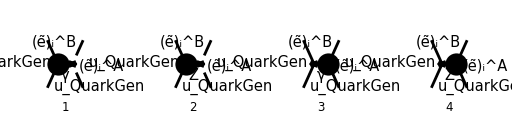

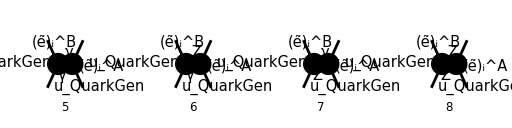

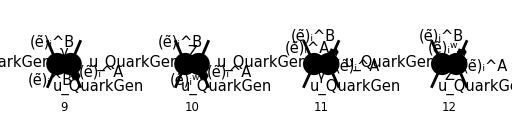

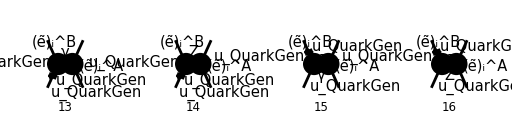

```mathematica
diagsCT[0]=InsertFields[
CreateCTTopologies[1,2->2,ExcludeTopologies->{Tadpoles}],
{F[3,{QuarkGen}],-F[3,{QuarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSMCT,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4],S[5],S[6],S[11],S[13],S[14],V[3]}
];
Paint[
diagsCT[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

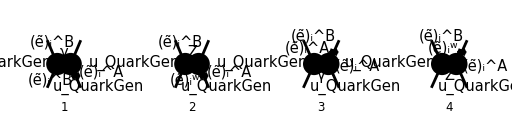

```mathematica
diagsCT[1]=DiagramExtract[diagsCT[0],{9,10,11,12}];
Paint[
diagsCT[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MCTlist[0]=FCFAConvert[
CreateFeynAmp[diagsCT[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
ChangeDimension->D,
List->True,
Contract->True,
DropSumOver->True,
SMP->True
]/.{MQU[QuarkGen]->0}
```

{(e (1/2 ⅈ k_2^2 (dZbarSf1(B,A,2,i)+dZSf1(A,B,2,i))-1/2 ⅈ (2 dMSfsq1(A,B,2,i)+(MSf(B,2,i))^2 dZbarSf1(B,A,2,i)+(MSf(A,2,i))^2 dZSf1(A,B,2,i))) (φ(-p_2)).(-2/3 ⅈ e δ_Col1Col2 (γ·(k_2-k_1)).(γ̄)^6-2/3 ⅈ e δ_Col1Col2 (γ·(k_2-k_1)).(γ̄)^7).(φ(p_1)))/((k_1+k_2)^2 (k_2^2-(MSf(B,2,i))^2)),-((e (1/2 ⅈ k_2^2 (dZbarSf1(Sfe5,A,2,i)+dZSf1(A,Sfe5,2,i))-1/2 ⅈ (2 dMSfsq1(A,Sfe5,2,i)+(MSf(Sfe5,2,i))^2 dZbarSf1(Sfe5,A,2,i)+(MSf(A,2,i))^2 dZSf1(A,Sfe5,2,i))) ((1-2 (cos(θ_W))^2) Conjugate[(USf(2,i)(B,1))] USf(2,i)(Sfe5,1)+2 (sin(θ_W))^2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(Sfe5,2)) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k_2-k_1)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (1-4 (cos(θ_W))^2) (γ·(k_2-k_1)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) (k_2^2-(MSf(Sfe5,2,i))^2) ((k_1+k_2)^2-m_Z^2))),(e (1/2 ⅈ k_1^2 (dZbarSf1(B,A,2,i)+dZSf1(A,B,2,i))-1/2 ⅈ (2 dMSfsq1(A,B,2,i)+(MSf(B,2,i))^2 dZbarSf1(B,A,2,i)+(MSf(A,2,i))^2 dZSf1(A,B,2,i))) (φ(-p_2)).(-2/3 ⅈ e δ_Col1Col2 (γ·(k_2-k_1)).(γ̄)^6-2/3 ⅈ e δ_Col1Col2 (γ·(k_2-k_1)).(γ̄)^7).(φ(p_1)))/((k_1+k_2)^2 (k_1^2-(MSf(A,2,i))^2)),(e (1/2 ⅈ k_1^2 (dZbarSf1(B,Sfe5,2,i)+dZSf1(Sfe5,B,2,i))-1/2 ⅈ (2 dMSfsq1(Sfe5,B,2,i)+(MSf(B,2,i))^2 dZbarSf1(B,Sfe5,2,i)+(MSf(Sfe5,2,i))^2 dZSf1(Sfe5,B,2,i))) ((1-2 (cos(θ_W))^2) USf(2,i)(A,1) Conjugate[(USf(2,i)(Sfe5,1))]+2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(Sfe5,2))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k_1-k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (1-4 (cos(θ_W))^2) (γ·(k_1-k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) (k_1^2-(MSf(Sfe5,2,i))^2) ((k_1+k_2)^2-m_Z^2))}

```mathematica
MCTAγ[0]=MCTlist[0][[1]]//Simplify
```

-((ⅈ e (2 dMSfsq1(A,B,2,i)+dZbarSf1(B,A,2,i) ((MSf(B,2,i))^2-k_2^2)+dZSf1(A,B,2,i) ((MSf(A,2,i))^2-k_2^2)) (φ(-p_2)).(-2/3 ⅈ e δ_Col1Col2 ((γ·(k_2-k_1)).(γ̄)^6+(γ·(k_2-k_1)).(γ̄)^7)).(φ(p_1)))/(2 (k_1+k_2)^2 (k_2^2-(MSf(B,2,i))^2)))